```mathematica
V1[r_]=If[0≤r<1,-2.71562984954227987707220753658717987150651086990482099679916347484158640580824`50.,0];
V2[r_]=-1/r 0.99895352636201278972478862820538575868617674167672469199326097337382722470925`50. ⅇ^(-0.99829411813147086629445907603814099626336482661084574202538457473067509617705`50. r);
V3[r_]=-(1.034069415130158819948746895533986389636993408203125`50. ⅇ^(-1.251248254822574068612084374763071537017822265625`50. r^2))/r;
V4[r_]=-4.20415644616125582469299138439140113373493210258692526366760104908016252690683`50. ⅇ^(-1.88979567639491639010430213789778028047296373449456361136288297937037496900499`50. r);
V5[r_]=-2.647828543053613773374298558957824633572173998851964865568`30. ⅇ^(-1.0017713271893313754426035031926440089474493688810307925058`30. r^2);
```

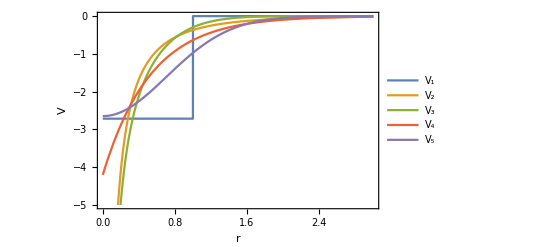

```mathematica
Plot[{V1[r],V2[r],V3[r],V4[r],V5[r]},{r,0,3},ImageSize->Full,PlotLegends->{"V_1","V_2","V_3","V_4","V_5"},Frame->True,PlotRange->{{0,3},{0.3,-5}},Axes->False,FrameLabel->{{"V",None},Reverse@{None,"r"}},RotateLabel->False,FrameTicks->{{All,None},Reverse@{None,All}}]
Export["C:\\Users\\ASUS\\OneDrive\\Documents\\Test_6\\MultiplePotential.eps",%];
```

```mathematica
Get["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_enV1.mx"]
Get["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_2_enV2.mx"]
Get["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_3_enV3.mx"]
Get["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_4_enV4.mx"]
Get["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_5_enV5.mx"]
```

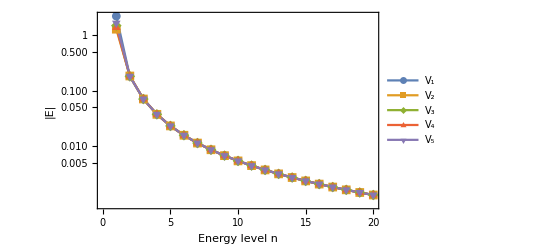

```mathematica
ListLogPlot[-{enV1,enV2,enV3,enV4,enV5},Joined->True,Frame->True,ImageSize->Full,PlotMarkers->Automatic,PlotLegends->{"V_1","V_2","V_3","V_4","V_5"},FrameLabel->{"Energy level n","|E|"},RotateLabel->False]
Export["C:\\Users\\ASUS\\OneDrive\\Documents\\Test_6\\MultiplePotential_1.eps",%];
```

```mathematica
ee={10^-10,10^-9,10^-8,10^-7,10^-6,10^-5,10^-4,0.001,0.003,0.007,0.01,0.03,0.07,0.1,0.3,0.7,1,3,7,10};
```

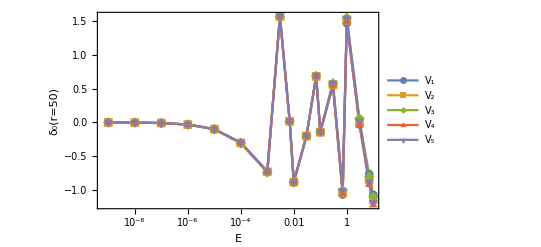

```mathematica
ListLogLinearPlot[Transpose[{Drop[ee,1]}~Join~{If[#<-1.5,#+π,#]&/@#}]&/@{(*{-0.003197,-0.0101114,-0.031960789,-0.1006096497,-0.13322,-0.73208,-1.319,0.90018,-0.146,-0.6548,1.2328,-0.5796,-1.156,-0.10646,-1.457,1.1606},*){-0.00101119981408722077528082082617036526315238287195986314755495831101348488278`50.,-0.00319768002352788218150070975322927977152981859287454515696631323618173642769`50.,-0.01011149173183073271917044192566952277641535934076088517546414586227654021414`50.,-0.03196078940512552293337350768758271644982874478177355495956145574663935027471`50.,-0.10060964977929146302920898313696792694331731557305040771702439861952307786585`50.,-0.30401507950111997826713021892165681010205303319686168605231949786652429811804`50.,-0.73208746431028526245311528777683686832243445809232317710518220752012414093827`50.,1.57076844873560063803161059293930907694661482058003836615255554636309742027218`49.04575063917001,0.01660417872846429221460158596852579979004601155758925173840829027950303459306`50.,-0.8867040276267463112271710911176501671747138924758859677727536648490533027639`50.,-0.20298505215399587250713295435250322849670206154991843494176226009924980256451`50.,0.68169074216635950683681615527649603106534146201228642284925341114335944777354`50.,-0.14617618177335730464091724674502957670008967138439070663660028352759711601404`50.,0.55098654513026699261247024430075427761020475265126615423514345605493842611528`50.,-1.06925978959202771287862387460298987714731106258899448437031943259989380615548`50.,1.47161864503671708577806852705949807570607304415231496709711131518438270067938`48.859846474979584,-0.03218782489395869862156094987340633158518392012124940662585627669497735709618`50.,-0.76629015970751542580591441134062613286861587284870400148883593814730113342808`50.,-1.0748683557181722316154300446515310649841369657651156422607286393748876811671`50.},{-0.00101128563258425921157579598302572887691743126610431664499189747986005912243`50.,-0.00319795140802972005657058013694390808557684798348064418629578192048748539094`50.,-0.01011235000674522048185488724485738596768788293303216956131604898658271272433`50.,-0.03196350609317015958320945732613624297819631944070120383132728608826588885455`50.,-0.10061832202777640843855402875546789112115337853743811538068627713913447280766`50.,-0.30404492419226639325731867851940898130237936605024753861494059497763394518555`50.,-0.73218616812544429244691233908324449275329261079977114259549451726850711390027`50.,1.57070216156980406107957954274162572886241997759512722890082113829724407161641`50.,0.01655751320254508901281443792541776374522950634083696337968996008482346335455`50.,-0.8867541573853743565790307322877934565620383473860098624664522617087292961587`50.,-0.20308391623460119181902399902605579493281184899884662457488626006155788297705`50.,0.6819292182463600706306160880944158652832190279181817494139352279040803244205`50.,-0.145425987043604289388008197668480746737288625979873760990148528286645582304`50.,0.55956397156694773124628350106136995203978741529876192866672698623585061293608`50.,-1.03996956566550532028489780863112361827590884463785016521787381101943866743024`50.,1.51379205220883323750927141095009509304949477115273500073462479198983445890741`49.14110566987499,0.01151465357758600083340349261198973207288087364649640266614614304158783200226`50.,-0.85176835394692940384579023395535525903163621248285647586612547315022675411653`50.,-1.14612125736993224687957657961137036657610756618317240796359156957887091362292`50.},{-0.00102671878817192855471841661901850262759738680776128677224103497143567862638`50.,-0.00324675544787806978978249276314448861220785946518636960407200088028211740161`50.,-0.01026668562130044192910682712240901875625024782258295550286850585043749677391`50.,-0.03245167451866323489669477655576634408592369606263899036405271438018874300282`50.,-0.10216562504626378407153741674126786570525103680313037473341796889322829651139`50.,-0.30901756386521594034884868237194699812922339086678825300171236517222592645545`50.,-0.74203191294269209185057964849708285899059425206037734681164434200614982098978`50.,1.56737368333512939861352932279842492285012662181154082998786741730488649416884`47.96967773980513,0.01552493437446682355125448774457949337102829018883158404330757865911300320149`50.,-0.88744319464309064157171705866912675367338695397641148397779471890639201777999`50.,-0.20224163362987639270492010964404402576249399096653422488822687792220870883019`50.,0.68634862737240553580258898698089378425666835497269542445588246323509058686962`50.,-0.13883946810241228030600565658635463959949715367860899012676600010950717759955`50.,0.57926998587076593877244067927595422948096119912435722147170771864141461527095`50.,-1.00801998404195477706308023984754126804421457879645551577404085225775879371643`50.,1.55005302476633452754316026791381766840439508759847489073287083050812477080568`48.67228056990135,0.05817699870602925875832152106255204051929963085551229989453681098439645923138`50.,-0.80667831867594189884072450511736090869543138572508425988655578751457094613692`50.,-1.10386093333770203615470799861251891799000305331485652907520330693451206907795`50.},{-0.00101128641842306435001488053067566566920074959750312933519266781210033054034`50.,-0.00319795389312098159777924567384642174912397042035665823805770424833259032666`50.,-0.01011235786689914050598691528544747158499882414706732919145880203899984558533`50.,-0.03196353099994213558006628549541926363627400959062837175190630117601910225526`50.,-0.1006184024012235241177997495743461091066015295861876175716039179245037346257`50.,-0.30404523064061299584131420827842479776341551966039290987567478446736200867937`50.,-0.73218818864413980852563796220737148709092927299679965076724073450478826948849`50.,1.57069921017157913745230985981210789177817907294073687119452578054790639679009`50.,0.01655287990685862097529993439524812391184369120353043493183417603250890293702`50.,-0.88676155322699035465597610067948784396837490388423506193552318405008058983178`50.,-0.20316806883625407759244658829433575182079243420633557447760466393044595719748`50.,0.68152055882262457337769553340136258946948049641742412594064188510291164067656`50.,-0.14616851862628250847675251201766201303321356306166012391319015467916699902068`50.,0.55479081458935396539221168434804941081019572710449090237335229306453726029669`50.,-1.0538847911917323343668059082008077617705426516002439364606350178772813813053`50.,1.49396072971024920974411635225794916801797721226807234385768702655322889656079`49.02634362641793,-0.03592064718849284760376889928374371756224493210141848650825970240572233576647`50.,-0.92206875556344505935305935047350379371892067042499774408594265240774201990479`50.,-1.22408623854611193461836840289909046778213185491918949114425971966649059757206`50.},{-0.00099560848778156251424398110282198110060624252552187626519308117574012980515`50.,-0.00314837576685031621115464466547757284694121688374782802674031229124372273269`50.,-0.00995557311953869300911291455831388371531743389358451032667919539963743938006`50.,-0.03146757800397505811656613088414195696019756216533039585492467919683874184103`50.,-0.09904522758094825673276441618256509045057943279394683235556400321388296621993`50.,-0.29895191927331823999104333018850765889282054602625597231845523128198985408577`50.,-0.72139357822496498258162694857794932533087720638821483423416480688444512278569`50.,-1.5664663903869268685896834390391042280003947298081106092188471174979410445019`47.7132500980498,0.01864676929204779498151184676504297395575013827775428072151516755689100710483`50.,-0.88477238714447337423379456595431816599593742697692623040641066876273129826862`50.,-0.19817415731935861300442022261937539434746976766289986580390714538818336146931`50.,0.69051521179668764801443614336171061496264949560835080852813071564472090435383`50.,-0.13486669995048488543524342013755838904424323553791863794799175741272368882613`50.,0.58264354615065219184680456281330485542216784342889563723459195825333361222496`50.,-1.00907963259076117649601970517585580140012215864542092236705945075165280323326`50.,1.54442050380934932144656226837272817865335610934634017658853905780342297997839`48.8792636457678,0.01802253356441921033297735546563623594280475318971572693152751906687531888132`50.,-0.88217314020006247603116673225789903000627072773560368016740170880819693726206`50.,-1.19051266093375012621531457746977053341135816250155897259078087611702084621387`50.}},Joined->True,Frame->True,ImageSize->Full,PlotMarkers->Automatic,PlotLegends->{"V_1","V_2","V_3","V_4","V_5"},FrameLabel->{"E","δ_0(r=50)"},RotateLabel->False,Axes->False]
Export["C:\\Users\\ASUS\\OneDrive\\Documents\\Test_6\\MultiplePotential_2.eps",%];
```

```mathematica
en={enV1,enV2,enV3,enV4,enV5};
```

```mathematica
AbsenergyVs1={{0.358617798575624098925425614921875478497728352905852778318`29.253601844585486,0.0057017539983845969396872998022555726128582622397629425412`27.452509272558842,0.0013569724797879980998341631406589399497920475947185192941`26.830952118161633,0.0005186729264264725552228571179264579664242661675773474436`26.41363838532214,0.0002510765234746596165907695615461150107700053548825441738`26.098667083445577,0.0001401250918926759760341834834843329046616493399375016625`25.845425063454368,0.0000860289726844717128193260875353062190581004716772117176`25.63357738083625,0.0000565594437932679305215841358391627788839348958006915206`25.45145057152529,0.0000391524386277650718551598518869446984669650594419076743`25.2917118184501,0.0000282157632938605343987467218350822896454001445548053529`25.149449553873772,0.0000210015056173053104805714845918177525593679406601704152`25.021211314415726,0.0000160514404396727174574364508803783257304340483446154428`24.904477044967532,0.0000125425581764817505224602763761691744787072128781526171`24.7973506813105,9.9862855585609418879629549631610021738107111238774571`24.698369647947867*^-6,8.080076435695141068164485359423216603629069772218017`24.606381964339153*^-6,6.6297465673586430763120297974667395414777483401231959`24.520464052205728*^-6,5.5067638011555916767389830830655111115380603015299254`24.439864061691914*^-6,4.6237438102001570258206460211081734135692230832470681`24.36396175920862*^-6,3.9198656701913759772521549473511601999039554106980548`24.292239486408725*^-6,3.351908581572751310417112135658992895712945350573962`24.224260713993015*^-6},{0.1055345144201990594885221544383250068694830579298273050901`28.67879221490987,0.000543467016943852733969570702928361088621031275186205827`26.434143196191737,0.0008787761850943100148101220384623620298373108077951657261`26.64246680327362,0.0003994781686331864048018368381859386535757218930026024531`26.300289598045698,0.0002048672094783537998752348303784811038040148581162085716`26.010353492649372,0.0001174746203905490358122975191711608706458281208073314914`25.76886303906389,0.0000732158622058595985638106618634351384578557935594018261`25.5635433893433,0.0000485835879005468302601033022355812196161560045343648163`25.385438489588424,0.0000338380136458268486444018061262982971585042925938410877`25.228360170145532,0.0000244902193477202638100479173119575232084188312719298382`25.087952043418777,0.0000182850794394759008131062122161739713491070739966003993`24.961058914768827,0.0000140077433295842578568459548205757281854590737346849355`24.845332096260893,0.0000109651586124814051898438103055965739952187224168095512`24.738980160440814,8.7426126585458211000594586322033895360045109020669133`24.64060744488177*^-6,7.0817320230005253335854311116018176611596491287278384`24.549106417558363*^-6,5.8158942969875257479898589492572767052914411999720274`24.463583983217756*^-6,4.8343920624132619777595682844655497848394460160196643`24.383309772964317*^-6,4.0617277439462764286493267411927933037836513321900349`24.30767904980539*^-6,3.4452207732166403314982030438771847873421902066836624`24.23618556526135*^-6,2.9473561593889323232654644655271122257102317749636096`24.16840134361191*^-6},{0.0491411241783143810174979817605259271357443247399920625153`28.390415091743694,0.013133066512374142958806801793404380414407522744254485261`27.811669658051816,0.0031008944764578472296754640577399589054927236857220415277`27.189112374092048,0.001184131825375091565373209985315138095978663933709140212`26.771856100263467,0.0005730505119519813645990613054242633435244143094321930551`26.45691410779788,0.0003197814204383386560369572745962789196598850874751940565`26.203684374509656,0.0001963170028581523752992092218063142509530970616778874948`25.991842668438498,0.0001290641073607252729115870055039587132010988792250973563`25.80971943818452,0.0000893412607157762201269420056170439681196255372785590241`25.649983282264397,0.0000643844698786331210902496918208123409736052442769139143`25.50772316761784,0.0000479222995041412221535715029902607970595401037021049196`25.379486841516854,0.0000366269062631123520316504878814101941904444016713572698`25.26275433475779,0.0000286201591855181791935648875731219117358596279483436123`25.155629619915985,0.0000227871510015429109532597165241790675418517565971502517`25.05665013835648,0.0000184374952462940026551123461980523089109187052882376632`24.96466391845628,0.0000151280849124582812685732440640510143600701192790542147`24.87874738783811,0.0000125656267212396593852628952032185162019237919335111584`24.79814870146063,0.0000105507226774086886080278162401695213398481341773493634`24.722247630125562,8.9445892114969701426315842993034747435523742820092`24.650526519754703*^-6,7.6486037595560809735742725702693892613345334147933445`24.582548845224736*^-6},{0.0291648691916889839337663128076661590872211743881346095514`28.151345084200855,0.0027543586812294695888166666176964201384168237949965603159`27.137795940720256,0.0010360398029298381790849866211979117879333799014942919552`26.713896731489857,0.0004266110227157877750631318665308841142069656067035125977`26.32881684153014,0.0002122844021241204357744621939634501140844985696826993329`26.02579590515541,0.0001200793408028509354701829244452247222934102905032125792`25.778386152775774,0.0000742854323875269117283732851401768922025558864575688312`25.569841399344853,0.0000490708492368483977234656902327914361577854030429285597`25.38977226775417,0.0000340760346390072795124535990570836086522640419150221182`25.23140425659635,0.0000246117529661936293192531398377545540070123872252636511`25.090101863043643,0.0000183484885804282160144218832391553980308493584416310762`24.962562331695178,0.0000140407003888983118228415410713516609831961947912356107`24.846352678721992,0.0000109815871999301197023686304553391118442149177469127158`24.73963034958281,8.749856881040731043701266075399768692777909176227887`24.64096715378524*^-6,7.0838133526001887114112281628139105325881900744423763`24.549234037574468*^-6,5.8150802617634928310346723229985748613271861840425127`24.46352319227565*^-6,4.8319897192753942827378123373993177368735268948013171`24.383093907427263*^-6,4.0585019504890652250964062242521935057580640953303438`24.307334000776812*^-6,3.4416225790619293562084413727545960700820262054198984`24.235731751940058*^-6,2.9436512996347736299990563605685011016911679692323745`24.167855088788283*^-6},{0.139407335499195184451569062496060704682802629665605891638`28.84325563091727,0.0133955441564343001509493046103860929126043087952693231037`27.820151374244322,0.0031378878473700722129188290637509764643845025113008014545`27.19424678782059,0.0011952213600777316677922748062959251530578319776910761381`26.775899582172254,0.0005777509056781316323280694446936844567109688448448890997`26.460459797709333,0.0003222012223500206081560349770843782394737254009927340058`26.20695728035094,0.0001977259456784199260877124892126238759442871172944318901`25.99494780288752,0.0001299568860257308908631982141243313816779821055684453999`25.812712864853708,0.0000899429144979530180418348121315700920048005639384982239`25.652897900660307,0.0000648093743933043549746015941981868284088074030199926634`25.51057968811104,0.0000482336325159569586779680104462593846939383303428871112`25.382299027481718,0.0000368619019898972383134328016833573854662113842190962517`25.26553173577435,0.0000288019307945647619677320544546669078020359934942256199`25.15837909852376,0.0000229306690303062746417536645301970518259655980131201233`25.059376771774485,0.0000185528062615269983883078828602544736962687625260809726`24.9673715564909,0.0000152221367020646281013491997329217380261645100039671266`24.881439011291313,0.0000126433496092034940058320174189985877517737842876530002`24.8008266604875,0.0000106156945302592983520258492495698451886572009542262002`24.72491380710732,8.9994578568540396939965213641877520881434714943948722`24.653182443503763*^-6,7.6953629916401752614948115456125499930184592155360086`24.585195772693776*^-6}};
```

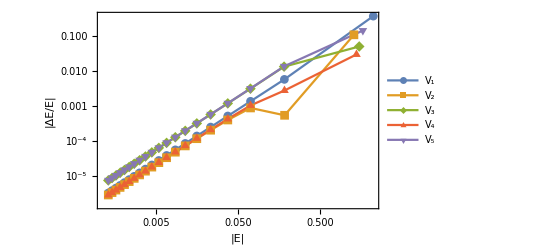

```mathematica
ListLogLogPlot[MapThread[Transpose[{-#1}~Join~{#2}]&,{en,AbsenergyVs1}],Joined->True,Frame->True,ImageSize->Full,PlotMarkers->Automatic,PlotLegends->{"V_1","V_2","V_3","V_4","V_5"},FrameLabel->{"|E|","|ΔE/E|"},RotateLabel->False,Axes->False]
Export["C:\\Users\\ASUS\\OneDrive\\Documents\\Test_6\\MultiplePotential_3.eps",%];
```

```mathematica
δ50Vs1={{4.9561475477440769936669073751235430186952659633488612938859326852`40.389277250264286*^-13,1.724003380653815124302522927683738858988587623833627263534362755465`41.4306731124541*^-11,5.5014910599922312475102335656514088510588937438190292808419183585335`42.43463517301017*^-10,1.741771742160420289282074444327745850782182629347228450314719697261345`43.43534362895188*^-8,5.5232890623630315872411379286083983642341507945190548698759326894994983`44.43852694770947*^-7,0.00001781516794912069836055368415520169452630315201348230349036212961820896863`45.4668520750582,0.00036534829736324755464316142945447198412094020029641716529935851964585080927`46.397005767847446,0.00041231648071266242670121814026429727068939191788014349098622219427737433079`45.21499892304126,0.00038775611009546277227860267344808300639783855204545068732242431567445408428`48.07241211593048,0.00047397281191287289364408915654633316545787447786840078311430088591309943505`46.42682869661119,0.00218103424347270150680377154191601014965867037763769456474723039142368764756`47.72784147198519,0.00527244424058428467174124028220890531141647120959036169886714639067225509328`47.589077355444,0.00730357190018487659779674823918369735939131472442345114379930653217249192806`48.38691242462185,0.0235557839312956405268656890696170826424635331986591523461627025148897809868`48.339310713279325,0.04789569464127563159113596099335216812303578870097078938440831688216414753584`48.340563823721745,0.06121827607989511251534374336631689939511515013370738282633246840911726863747`47.44978989385812,0.15823254651771847122308339601371091917104314663008248590947736171574986086368`49.85175466669713,0.34342325101756896260188410204069292408556825440011799424653205402188974080894`49.262596034556196,0.34228932720179853767793463602603198782075190954562833902696570919539225081232`48.59113577278008},{4.3750667340594568997747368856824042024199539843134014404035961504`40.33508084883238*^-13,1.521873587959555062180527491508125336885534230074139974343056505108`41.37647672276786*^-11,4.8564732558067910176737685113070643260778872440315467849971395487746`42.38043890244549*^-10,1.53756350093681981962567568688445968076909982902518035469162803030849`43.38114854970048*^-8,4.8758676281436554279289040316971452977000003564211877551429814257734236`44.384343788290145*^-7,0.00001573141583208734959368753059928902478695826178932519328236183123221592083`45.41278882262327,0.00032355705907517023646953034848301589185743273168960373931939673567419621579`46.344203415412196,0.00036742702974340754072182352099002268683294860932777441445442129642550250537`45.46598044540049,0.0003496993903949692558438966963790115540433049050572566144657161322491459927`48.028280368442026,0.00043119827685866200990884445439455998292483510268205309587992439279716196267`46.385738209287986,0.00209336421322657503498833867182497754448042851810099236180368678361389037504`47.70990669125839,0.00552233723994963834813473190602750692375136897530216104620987551249524129811`47.60911568206293,0.00806473827739106737770959483825349209307103329714000338824232077108940835133`48.431040080898356,0.03214460448038377676874977055889528011159875571981745198547539115003384860909`48.47088519915833,0.0771959188075152180439881702239205117908865131120676389730842929980251148395`48.5537170051665,0.10340086411700177687481860752307872203788443844741856887192913662470690624423`47.92289374202653,0.20194223602608080751155712302664501925180743637148753146797432605510500815789`50.,0.25795055688729895172732966131109899801812414174476161020183902901228697798527`49.11895097704546,0.27104122703147443896145031235781991859815575764888588620809588828751491020181`48.486265392363514},{1.10333124323015819613750684755510515471230477213900420717167633922`40.73022441109767*^-12,3.837954845745044086302689242960938298618961490285811679989337600416`41.771620284715176*^-11,1.22473673729380225574929437973390357599446018266638575694688669248198`42.77558246001175*^-9,3.877568173184429726433826319474771830084135094297298435500168588205042`43.77629207546827*^-8,1.22977488132235962613859780055046225103842449218630342084687239434063219`44.77948821232873*^-6,0.00003972901418327016651856030636299745946499154797822358170828287797661824318`45.808066711941215,0.00083245627588432414523411194078783143777128126656858633169580176002981952827`46.74866531192224,0.00094562203340018643264905407318252023744429219454731710427850274516628078107`44.332447367577835,0.00088631728558550746785053989572685575197207250948976703249545488384698110129`48.46810674516612,0.00108177825478392462067896897521340074137588807102255380021783219138919809403`46.7847030700666,0.00497492444499802165756960124865813615678940630258507081163170454091802232041`48.08457692530839,0.01202013270550570102775016365226658415389158250376020236763197647880849492376`47.9461541796518,0.016648952302946801952768424624235927740993322909877510741415276322222453833`48.75255549427271,0.05392560190438877705094768103758736226308015502943147997332984029176139301305`48.688584312665036,0.1109667543639743081381819885060877267298120637132900549208853469952145679648`48.71742402115975,0.14133388616295129593561291760065955739119320554630716480251684847901830312264`47.614007400444,0.24991780932431713330083214387045960212540237977438832958851563005121984234773`50.,0.30404219166881892819318638993609791172570348820394445962899015537202221146436`49.20022139664954,0.31417591625279289843116175090008801673336584889712894730377996198292086399629`48.552439431728644},{4.3611810707344588292431105998726466018267353994039201311237292575`40.33369994794419*^-13,1.517043418835955805945621263469951056128454704796418664453129825902`41.37509581611691*^-11,4.8410589891337478090194735885016424642916176422933415960320466291244`42.379057938080116*^-10,1.532681295747542171852260922636837216225656240758138921719743799300254`43.37976700803387*^-8,4.8603208069807142504823496941392564497101395589954746350143007881142644`44.38295647396483*^-7,0.00001567917496632341539481273582628376305720261082831396299881308598122069159`45.411343817701,0.00032205772124624438280529934680639956877558362014526269091220211359951602512`46.342185498180974,0.00036467158630020641732070872097580468830153100837303204527590134899579394966`45.462711378394715,0.000345144931240676538557927547257928360400393462653046556192358788288544565`48.02264945535357,0.00042386979159059875401406443778214125696889473709569875940806622834011593536`46.37829183180315,0.00200931412257759653730296112908630961447099293858563339185895092457367250301`47.69202011399448,0.00511378236775691665763504583846629816881502945920344037156254700873485045727`47.575865710569076,0.00732230716873712992879674007485783982007991065700561025494055293551960499208`48.38802011840252,0.02737155184568368617508250878975356084427203499427303408627062597158963597696`48.402987846998094,0.06328078485966258060941919359263141251392702218680248822825898978328436701136`48.46460195801757,0.08356962569327724234731380305437447504842629378085434485168653894874959057964`47.73253786222254,0.15450700129590712234581592639344009467354331667467661765288920759946630473739`49.83417093497924,0.1876502056386574745058061279927154308382586102808442319463095070877736002605`48.96547071422033,0.19307628982540344819428531478874773656596451894230965390220580908664122651713`48.33514825907351},{1.16590508613087792972612171384186441706087361403149921802475061495`40.767544610539346*^-12,4.055617851241444437280324095521611577648655695999330058518573290131`41.80894046656145*^-11,1.29419213439086121083422360604689376227551999887206082589766132020648`42.812902465703026*^-9,4.097357805105027164447048163062994352399132728627893392546208648091725`43.81361029489035*^-8,1.29912960517465566548832302522397722693535009306942604397474457539155877`44.816786081689074*^-6,0.00004183770309388037364591685831611871078982501254475694596027297996442792781`45.8449061037314,0.00083962290073706219969130919534008818732449214821181757891569458186410282021`46.76462934581845,0.00094072182927718348796397013806971897699251785261405922734269101456535168149`44.11838118244695,0.00088721353085461251359714959756501779882298902632997160344891383890102363187`48.386851314237454,0.00108613988351434146022981670655951239558388339216417436394862521481913826201`46.78775771898923,0.00498427600587641229119271790370968495038054114938632555384231077502648583218`48.09409765499641,0.012047840848506896890541369180936689147734365342002866778866207878892317292`47.944511299142995,0.01664425395782393144138855968950905679164935508179085806732329208513229852493`48.764325206812735,0.05316853297559127939099644960344567112460860896711083760730546357918126718075`48.67950358901074,0.10628178383952859943353256766346108966602897164523647242696322840490019851176`48.69921415063989,0.13237308491612572683214608967300573323200338686055314141398468571488926935436`47.78322320744521,0.20714917509283301547423813601385109168308533332301164862589097045540959032445`50.,0.22655345360552291204249303576090698144564052702513745206148490380214499685289`49.056121298424465,0.22578354109924464783910945285844851337312289526904420966185166596255513843036`48.40479080388884}};
```

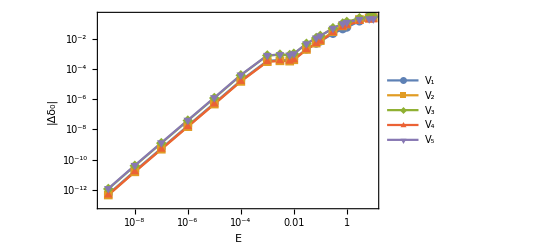

```mathematica
ListLogLogPlot[Transpose[{Drop[ee,1]}~Join~{#}]&/@δ50Vs1,Joined->True,Frame->True,ImageSize->Full,PlotMarkers->Automatic,PlotLegends->{"V_1","V_2","V_3","V_4","V_5"},FrameLabel->{"E","|Δδ_0|"},RotateLabel->False,Axes->False]
Export["C:\\Users\\ASUS\\OneDrive\\Documents\\Test_6\\MultiplePotential_4.eps",%];
```

```mathematica
AbsenergyVs2={{0.2927657392381089783183684157192151738176181146295063331331`29.16549025660482,0.0064463511133989639045688116943585113113019527574773996495`27.508283960873623,0.0012514656093235780854532012798285671553430149354977041303`26.796388923892554,0.0004497260766804232868644871818034443147123641176165080662`26.351918074537,0.0002119580189872289904531006409012489245349536572026859898`26.0252198561722,0.0001166527606369953794013242923705017910277778823704747289`25.765865025350287,0.0000710332673611226273648548078131840832747426590711047027`25.550431795979357,0.000046457250132893825978425445015175983853496275361180011`25.36602350408663,0.0000320459974513127969307652458756621241908084202542482259`25.204743798148424,0.0000230367981791572970935809741971844379352728675840603816`25.06139212189306,0.0000171153342999491747225817834290460593378150897298009241`24.932355390614784,0.0000130631669855103805935117534945697527394699719766468984`24.815018482775375,0.0000101966179540688728100557425693906677331012943861779419`24.707426151838405,8.1116165429098090379564516020943573418706847937822211`24.6080774165873*^-6,6.5588014958702410881013547921694804002359551509288447`24.515794491381865*^-6,5.3785589775895568046463318680590349358297308750297833`24.429635939498773*^-6,4.4654705494676650790602910916033140852505316972307642`24.348837233802424*^-6,3.7479944194053025288175391031751258325795570303006418`24.27276893990734*^-6,3.1764102351066042914313802805245082526592925966056408`24.200906591081527*^-6,2.7154294766694931454428302127100628886257641924412055`24.13280853240335*^-6},{0.1605691623098750529126893072273511367522519583996186707824`28.83996111933141,0.0065236664668316363278017790120184209820746423397398096364`27.513461753252788,0.0003976620076574059681325661502188069459915362556415301752`26.29848410512107,0.0000737547774825988277922905586230403977441068381644407556`25.566760161421875,0.000021310661813833219319115365467828758090128236657641965`25.027566941503657,7.9320984217851591000644723217901335265896235870739601`24.59835809864551*^-6,3.4850203377345112370974111395508627580026639765798067`24.241175321214836*^-6,1.7221881003115137165811456097790417013759814536604584`23.935050588425757*^-6,9.292228447897654572877533395239374791573691593461044`23.667089882653386*^-7,5.36784142408521739987790253634759967973341336330471`23.428769681828175*^-7,3.274770843916271038091597299735144160647115663618098`23.214150919441032*^-7,2.089080167828175266280110941438214042670432232953156`23.01892511055728*^-7,1.383232434239417137787682316520484940253682956914831`22.839865168122742*^-7,9.45192392346933836127634693663693761887192581142164`22.67449022176626*^-8,6.63561789543958186665825986167328183284552766728987`22.520851374051226*^-8,4.76891256483748340922590487942365115510961385217607`22.37738936431304*^-8,3.4983800232193742573723424487714388377020255004222`22.242836988730456*^-8,2.6132459092300668272495531664957070830250184826351`22.116150283560724*^-8,1.98375908160237073815672230128693246425454119851326`21.996458932293386*^-8,1.52777601813422069516815591208372181461771366694118`21.883029692856763*^-8},{0.0745800463415433183424628137736116814466628597916051955309`28.540353881235852,0.0021507520022428083521325854441184147363383259177899991999`27.031560340215453,0.000187929722171543164095984796795244527781411158788515478`25.972965476050625,0.0000372987870373877742747024276507241772189243721613800404`25.270664713047257,0.000011063869841151297038579143619918846792791767508420548`24.742877062290287,4.1738423623779396870781398562681591303940483714408898`24.319506046947055*^-6,1.8488619682060198025530666434386409215142198911159182`23.96587449327554*^-6,9.188312726939753265932181993232202760836919759665602`23.662205772451625*^-7,4.9791727341364178572372189791829897264299740072058`23.396127197127054*^-7,2.886713791771991911880186766481304689028572930569223`23.159373731474165*^-7,1.766755964844972655779694611260467498149841361343716`22.94614657057148*^-7,1.130443153843902869420000714513705103606792144393919`22.752218732368444*^-7,7.5065963577254014367841228114886398055020928347261`22.574413068087644*^-8,5.14411473517396423524711230373688501912720203419397`22.410280650935167*^-8,3.62179383034360057720897909326903190010789503395613`22.2578937289191*^-8,2.6105823781727271251050483650743829611097835025066`22.115707406468605*^-8,1.92085442924793810086382851931460538555558572564756`21.98246445770898*^-8,1.43932200370858531718098752513273055347076594518618`21.85712796907853*^-8,1.09613144840443115539607365782013174679333834169826`21.738832642328887*^-8,8.4699107443158529842105767010123879530979178370686`21.62684883810765*^-9},{0.1559009392376804870620149369418100428221268745213754121383`28.8288981193519,0.011674048143582157414734567996173535520723242230767542762`27.76619148433714,0.002084569476501384165874693990893296073662010840432664499`27.017986378616442,0.0007330248084345833393252564001891124109435168795188886979`26.56408867745453,0.000342333956640940348678884732795049677652013197821021514`26.23341998395991,0.0001875179283618426694735970585840059035994371975636882958`25.97201280075385,0.0001138702830178270855632014188071837622555069133533127215`25.755380404400427,0.0000743431094597949906045217561670130617786528845545654205`25.5702107261884,0.000051220929375884996804003848966325161955921716524462614`25.408417458576917,0.0000367902750415859370360472731403960120279766342988966499`25.264703038935192,0.0000273168489866337659645268917804199698515840628787692709`25.135400606130247,0.0000208397863180911939420522166412923476030462473696856369`25.017863265923697,0.0000162609536736751351106932908432666085828922623830594681`24.910116016877534,0.0000129322790014158357540738252191444214126334974245126161`24.810645069860154,0.0000104542777776763930576179971756665987857086268403146847`24.718264039767668,8.5714745060485073809374381956548809925457194081243754`24.632025542100234*^-6,7.1152608295934125885749648279782047041581511959923114`24.551160829315265*^-6,5.9712795154854320199420367309635354610447567813280982`24.475037405310417*^-6,5.0600934093796077118703979139858674223454900018480741`24.4031285383307*^-6,4.3253461045067438328171992383139034380656795194737244`24.334990868798933*^-6},{0.1148192632377423254379396909578097949875586530267615474883`28.758984760133515,0.0098577045115683439890563861284962000925637556124695690958`27.688485617018543,0.0023961527838319423656527548123953797553824671610190497655`27.077445119323684,0.000920941623940385036820215367151786435070072248558516199`26.662802330815428,0.0004467701161737057798206191177314134065084789955872252983`26.34886013393678,0.0002496042261574703095574292364573847169528270885601615184`26.09611355042543,0.0001533330893236572058512432268692564576158523350431683871`25.884539303565525,0.0001008444037185584810552192881680983130038538057058180244`25.702578012760434,0.0000698243138310132886471548297821165071668561428322135288`25.542946357628665,0.0000503279011694921667927437805161572439737427189594947434`25.400756967096083,0.0000374642091475544475297161077769286818502278228009797468`25.272570303413037,0.0000286362495544692133747155815993157921664972835100586866`25.155873706429198,0.0000223776921607285709086538904050775316244391830985223978`25.048775581107318,0.0000178177930230094933984668129766907545504177592051140135`24.949816175965438,0.0000144172231292852419794662816228498306537885860413333689`24.85784536296135,0.0000118297604612301074295595562943900565862137362663891979`24.771940817529963,9.8262051023982668603306777335818833923386762843367696`24.691351561813306*^-6,8.2507145417079534450939357228626838034572755289340837`24.615457982761896*^-6,6.99480974571730422718684016227478609292530683950706`24.54374287299998*^-6,5.9813970198600399537399932035637412703597810373616652`24.475770036657526*^-6}};
```

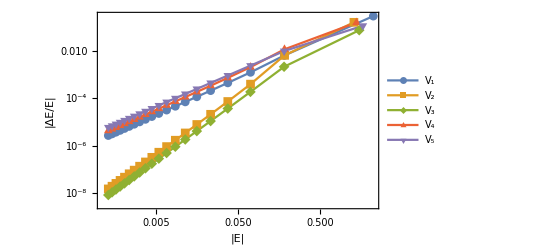

```mathematica
ListLogLogPlot[MapThread[Transpose[{-#1}~Join~{#2}]&,{en,AbsenergyVs2}],Joined->True,Frame->True,ImageSize->Full,PlotMarkers->Automatic,PlotLegends->{"V_1","V_2","V_3","V_4","V_5"},FrameLabel->{"|E|","|ΔE/E|"},RotateLabel->False,Axes->False]
Export["C:\\Users\\ASUS\\OneDrive\\Documents\\Test_6\\MultiplePotential_5.eps",%];
```

```mathematica
δ50Vs2={{3.567861569750689605931887310118242459942533262627047127816339251`39.246541018995394*^-14,1.277786141661609896054045534720818827457054287683453981228831120921`41.30059317502485*^-11,4.4092287351769821085936821153530309071662551667892342455330762407444`42.33851741180398*^-10,1.406356740262793660009587868178780770777635341623147903312967401862827`43.34244810137055*^-8,4.4629099936177378041177134224308892143677025987552003168584984079816246`44.345949458575454*^-7,0.00001439444494282516533219106448570182773399337894799147785377737403144865197`45.374280083166994,0.00029467550780722967937810967090649433038267289467423810050543635751181440292`46.303838488166534,0.00033108271958863390848555561285638620325769632689131107383422367312632491777`45.119702375405346,0.00030896196796376191715501835711856975756486003998283589177833014395055645733`47.96463574443598,0.00037557860598867848852520119328865649912918497067628343419786237920244568945`46.32598415501761,0.00166109580169446491713664262654860685426513898360888943418649446411621542243`47.61368126252218,0.00372183272520683432990034363537116248777765972650793207936978139578060496589`47.434955513165846,0.0048584673026925625762682016854742011933613225367283833566901570464561996095`48.227870655631634,0.01038704662519416170693389858079262966362715885003462457854750011045676430724`47.97024666420982,0.00653394381006744032445587200882927889942432205394042951597967521897649264487`47.486391121125436,0.00159087972501860656469598321973349042973991069737451054151389683868880756055`45.7072603691327,0.09675943778473700522619720643132215684659893460331844681676531693316252316051`49.77850321681525,0.29131688847507867412201442373799150593104171423549140212337177962366294189316`49.203365304156755,0.29540695637995149831819612657067208980483308037851155011045008134915162042298`49.08211633627861},{2.154560961111445601546909987019654799146`15.0274549536269*^-38,5.4502786667730486261065336544313974546312069316881463806851`33.93051685170297*^-19,1.9154491056401669566233534663610482015871750119634522983301417`35.97638852848826*^-16,6.120152065725935680241900357447378627587354820941938195423270544`37.9810778061736*^-14,1.942487000704569918612347048015032027398115264531434794911799855464`39.984651054947875*^-11,6.26499835528971251760982526500878013453464243007529523074311697384308`42.01295320359886*^-9,1.28245545545471115008109546061106635790950758675436130585094092876742666`43.9423903930641*^-6,4.32241319226961801066263118977425485785170658886371535292871675411144425`44.13860304052457*^-6,9.40403080671583330200299945260411382016875261102363753484972265903815183`46.45341228628232*^-6,0.00001631943820879889617107324404006456036324841534817439290721709384066346526`44.96386797904451,0.00021614902656377716452578919962208674927053113729979158037419084299251573675`46.72581670305441,0.00113106411704696532780409229326221945761838742996971295666594111373345158538`46.91907824518654,0.00212330187113129009455900388358763226048873681662804865302143366656084104374`47.86018077046931,0.01550264867305607836960408553540678410743772990552669141100857154376454638013`48.14758425929495,0.05030139432358542419079725662952194352956502402063565879164147302116911132822`48.37315138116023,0.07380306786617919149879962513276175727363664170977961214962763918555350883943`47.59712218046092,0.17114249045591117954081336892462995470285525017539465090878830830776935388761`50.,0.23181684349095919249826579267646801292838622598445567094814630977209426274513`49.07838467426749,0.24752860100462864933402674934323916535247831286798221417903946774282293248944`48.98883080752241},{2.59088758865151240941970337345284522211807018310608616658157`35.100967065557576*^-18,1.2149053010353933727228182753274571393246280501356235022292938`37.27206285344495*^-15,4.191204890815656351760507611552444656252236623330155536684413136`38.30987863297776*^-14,1.30813899865298605668162544158301983672644502017346728893340263312`39.30438678604926*^-12,3.23373361813183429496286325436959905585622967869509835796611282739`40.19936944968229*^-11,1.92180457543384930624408529914909114619947690797567882061353179252634`41.492696061552294*^-9,6.614731858493500750389481947106064191100064057557992366832905999116574`43.649059471036736*^-7,2.31492197860834271937785589336800323432282224984391959247376328585042906`41.67426795531048*^-6,5.09056388561637699952768481215934314727738703814642229608748754748568411`46.21477733097116*^-6,8.87816893428624819725828488240770745398813712860071997764650906217135232`44.69915067313261*^-6,0.00012114095890005822384265655657109667299310625208815892740721501951298011124`46.47626039687389,0.00066789022315065975029380942105244141650974575019892023041260765193903794005`46.68734167978037,0.00129589121594053712739428085074600997574773006295651525695646085672439614425`47.66700352846552,0.01111813688611322149481299164783120898449523305217909121167485692410264395055`47.98630890672523,0.04254881617473967153934588421273626365589800612302545170151486510259587232963`48.31531787902604,0.06653933389374460897008695649796779373115014949346806943941386581140117702456`47.180868533410994,0.17315422802374647038125430847894285598501112630017445469434616105683440716457`50.,0.23900840439921955203355508949198391259832868464482381422061289998218051791321`49.11068659628382,0.25566145401203692829672176150092301572003700269016779487782172396205331860688`48.65909149920263},{5.640573132111307082174033991184128415422372010689128690048055709`39.445419064028705*^-14,2.03327155459452708518837085042193129187658393724893050821429948109`41.502293192680774*^-11,7.0165331817622281182515861297397182312639868700385453086333646059927`42.54024017228187*^-10,2.237985883904993081096956753571045974425259040525019508362945424994401`43.544172749614795*^-8,7.1019627584575443068129466767331642722263694488615373816064690998851383`44.547672510229816*^-7,0.00002290538467148147344563489183703356740271986882128509346378999142037150153`45.575985757907425,0.00046868982013789489002749617976460025202716585236119489543748396220095693785`46.50537182940445,0.00052589934165332424503799302930888837132539939911631754106954079307874902024`45.62171093861192,0.00048949356861222048235807298406870565132019262317959681919590267271981371448`48.16346906906531,0.00059390772909860886894616765049217043584634801154122388533007473020109608752`46.52502758465316,0.00259285315803375145749334144286280407974895628511898139461807269473330282988`47.80767261015954,0.00566293537667307888525844320667685141902845091807065267484671467885515121999`47.61673205235114,0.00724683950627584511714982495695154108110835041027992801337099485557479568184`48.405166358003676,0.01323421406830733605301715151915984154088758635934767147751908573161949191833`48.07138962321547,0.00163737395295121593712933521727702915585514866994456505795887677333719129684`46.89066224771784,0.0125782600309295037021052434085406664202657305733825855150459490500699668684`46.702263047949465,0.08157850577263620148858109598577290955242411953158807649961570518733727941822`49.72569433364537,0.1258524811602718124161520176547530279686134573962302353976771504577329740166`48.80539776209552,0.13747221705412737396091701610361071206499313098581010312413739360251355287098`48.38026975523182},{8.935041957513216753706810534689315642311560020315017534909655031`39.65197801013127*^-14,2.894830761286838840664614191498461267825985419575655897246015904256`41.66250662029496*^-11,9.9805970766875139053557770646459116652918777806179330501154664535189`42.70006023933174*^-10,3.183102517016174870585006623478350242753323064196702762163166209711636`43.70395709326124*^-8,1.00999271079818315241376604062197208971415804513812092059009869327688351`44.70745247525407*^-6,0.00003252985243144679838413405586405245894467072314880449220512573563443292368`45.73562712375054,0.00065295600148438316708550118628815431866637593015124076867153758525907314708`46.65548514799462,0.00073178668169561534679533964105846062121595998749055197776069463698349382571`44.13935440902138,0.00069077590519548723047168896512234930121465825287094491781549164310047496155`48.275823314607315,0.0008462841207389034834451249921181699364089609076937689553411165121021157849`46.67944698459838,0.00389934891525877279700877503825741942425351637112776375764117373514684381347`47.988663292361636,0.00950730232250224102998796251826162333785558722344227603468335441258878096623`47.840854170869335,0.01320752319701718222151461665637724345192875299573732216398978338271774898009`48.66912561604567,0.04353567536759005173309342649691195165590765244109973436359679508842361494674`48.588948659262705,0.09067717696288742795177661745030098248729800752476306558400083233374698755693`48.63345509296261,0.11517362141456311506007808256701204260708998470598394808960275396308225433838`47.56653077903834,0.1891890022663402069768893295717942271206535137775241954371006316741031226019`50.,0.21130459494608835893899895288118006624037234685747934354518880656935199701394`49.02919873992094,0.21206358242765137745217201511002229056762025658069716457338376220277087942932`48.91264868689532}};
```

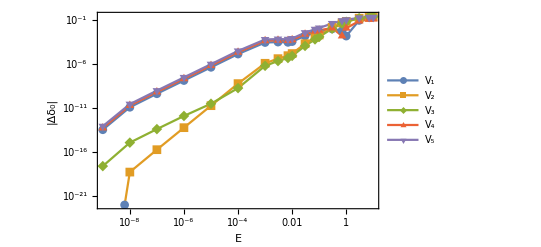

```mathematica
ListLogLogPlot[Transpose[{Drop[ee,1]}~Join~{#}]&/@δ50Vs2,Joined->True,Frame->True,ImageSize->Full,PlotMarkers->Automatic,PlotLegends->{"V_1","V_2","V_3","V_4","V_5"},FrameLabel->{"E","|Δδ_0|"},RotateLabel->False,Axes->False,PlotRange->{1,10^-22}]
Export["C:\\Users\\ASUS\\OneDrive\\Documents\\Test_6\\MultiplePotential_6.eps",%];
```

```mathematica
p4True={{39.65253582644337988096095180117538405402`6.,1.53907489342902585463081319858450645293`6.,0.41247172299636746548825756197336252201`6.,0.16554037207357019335030590992994745796`6.,0.08222608183500403742765543386299084336`6.,0.04662231701660066135669627562017448598`6.,0.0289309188216409261827098805192826829`6.,0.019167303217541028505356506191538984`6.,0.01334536772833940024767854303592237013`6.,0.00966110612935346499508694561675381771`6.,0.00721705443057085025900858998602087338`6.,0.00553240772913182338727927137573036059`6.,0.00433374512980545378461452729376165535`6.,0.0034577505004050864005043843378122042`6.,0.00280277326814842881530299180830358209`6.,0.00230328886976090998881224112102305501`6.,0.00191576589578912467337074107637119937`6.,0.00161051441082978095927206041699011693`6.,0.00136681208879429642980614001128810694`6.,0.00116989695719458911225599083799540639`6.},{68.88682868572038899525815497756520358644`6.,5.495025535074949730736023531795857309`6.,1.30770145421138107495818595128790420773`6.,0.50657955080496104858300603983502835191`6.,0.24720288867772811897613242810205961865`6.,0.1386751955041779808961458982792151365`6.,0.08544088346421800725309112650220339869`6.,0.05631774008232106160293651301597870069`6.,0.03906145010955400430124600831411727612`6.,0.0281934110473481320559355605209451888`6.,0.0210108008121626470674129037947206987`6.,0.0160748577970012160144165209845116046`6.,0.01257152963129365108167601776875257818`6.,0.01001657111227724525159988380734446791`6.,0.00810960379985230111821292100386296323`6.,0.00665755561732039549808300957560132614`6.,0.00553247177309938081769590204280890713`6.,0.00464726668950713623929704436075208836`6.,0.00394127020504051208214844922333544357`6.,0.00337133251119112824251749255329175991`6.},{98.45362228616327540609455612150923573415`6.,5.04807397835986489722826258102258716973`6.,1.27491212870986306111404271989566297891`6.,0.49858175048203951817075122126671885043`6.,0.24412427319348843545896095715351097618`6.,0.137168260032577291637889720424474088`6.,0.08458800825120242009668104175062541181`6.,0.05578633203694524126940075091704568457`6.,0.03870702765372613907336386505218802473`6.,0.02794475433779497233151894890573837434`6.,0.0208293846439425542525147855994319155`6.,0.01593830757861510135092710321400933844`6.,0.01246610116299490715841767611728459832`6.,0.00993342983279752359902784055823002999`6.,0.00804285404252801587975443870427974576`6.,0.00660313715492008484965495539406909985`6.,0.00548751237665864294721649788362366221`6.,0.00460968689997684319581814064140896373`6.,0.00390953385486748316373588581235600287`6.,0.00334428443827161380392994396217903805`6.},{28.88557523053066235396668549507332053735`6.,2.95133869907903869598015114046677245166`6.,0.72626948671767254863629632395806984178`6.,0.2841973401623147208076140190979006934`6.,0.13944671992946253771711149731340442739`6.,0.07849884341946450573082612914113324281`6.,0.04848128671705138574086735427339697701`6.,0.03201244634735383511735541405727144136`6.,0.02223346209090080076989625043344914821`6.,0.01606453794023180281584980010611384011`6.,0.01198221523665585593683739415747705537`6.,0.00917382642173330772659306612125165176`6.,0.0071787851156061341961131151306732936`6.,0.00572272560231582528684486721530033986`6.,0.00463525905443525897433967882977435827`6.,0.0038067567356183018957026113406901081`6.,0.003164501906864473819307115350866091`6.,0.00265896681643090566688499533368194206`6.,0.00225562418040471609274699593484750102`6.,0.00192990310221970067351452099963259516`6.},{26.67133690813495930967552020289486897459`6.,2.43802221703123063502735629452523157695`6.,0.64074691475835510002426356539697767423`6.,0.25424569666467302536992207536698891355`6.,0.12543413157851992887718195113110538157`6.,0.07080723963517916339962655045802162471`6.,0.04380255983028453608608530681840644574`6.,0.02895376221138428103661835568616616185`6.,0.02012392248290590330651635800792584889`6.,0.01454810650699973735963141810353172819`6.,0.01085554145939290366949009379530012363`6.,0.00831385277371757404858091745577536788`6.,0.00650747745542058978302817499342514418`6.,0.00518864957823754160825618939651505728`6.,0.00420339203001655858729585853497305106`6.,0.00345257986250563355550701838461571294`6.,0.00287043334883701422570003007470623666`6.,0.00241213243859014037184494899958866065`6.,0.00204642161333868367697756957483364465`6.,0.00175105235108427634043841258909438758`6.}};
```

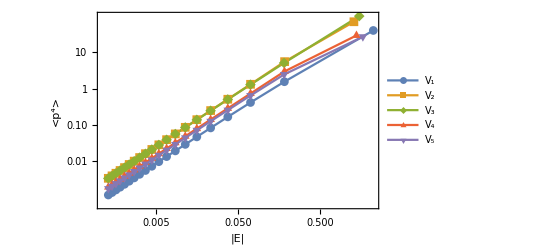

```mathematica
ListLogLogPlot[MapThread[Transpose[{-#1}~Join~{#2}]&,{en,p4True}],Joined->True,Frame->True,ImageSize->Full,PlotMarkers->Automatic,PlotLegends->{"V_1","V_2","V_3","V_4","V_5"},FrameLabel->{"|E|","<p^4>"},RotateLabel->False,Axes->False,PlotRange->Full]
Export["C:\\Users\\ASUS\\OneDrive\\Documents\\Test_6\\MultiplePotential_7.eps",%];
```

```mathematica
p4error={{0.74571638479093026499710719069607628865`6.,0.03067233922636721249736811053405380919`6.,0.00406042158294931559206278124263474738`6.,0.00106894694492632032969108989426690716`6.,0.00038015005404110532282269414955296943`6.,0.00015911594725399344106644119135567645`6.,0.00007338549540642224101562617498872837`6.,0.00003590799619492142401336222494416239`6.,0.00001817706571420960098005118770467917`6.,9.3383994464951352523987649828024`6.*^-6,4.78733655068005525492841664883509`6.*^-6,2.40684966476618134086712982161784`6.*^-6,1.16227974358705474473167483748036`6.*^-6,5.2373971633894975622183664776968`6.*^-7,2.1013110317160769861866704103944`6.*^-7,6.846746972883712279894174109183`6.*^-8,1.412543215058730210434292327604`6.*^-8,0``30.,0``30.,0``30.},{0.17376366582436478197596164449809670617`6.,0.03509985285751717698106240851092187828`6.,0.00261820949087709907938665124198786694`6.,0.00058020311194763871931204598584898972`6.,0.00019445353000185713024603487214212425`6.,0.00008162380737680982735581719376505357`6.,0.0000393228909679956414083101687071699`6.,0.00002069990554904823941511015229748244`6.,0.00001153866292556273768674124853026513`6.,6.66219349564051007865110897185901`6.*^-6,3.91197388043871313341965204258408`6.*^-6,2.30040000737063357649664281581251`6.*^-6,1.33029810515298033342204137207535`6.*^-6,7.3931143295328111411681211542598`6.*^-7,3.8116583280463123476832765286909`6.*^-7,1.7022715294930662350729431537184`6.*^-7,5.416231744541099401008168687746`6.*^-8,0``49.52287874528032,0``49.52287874528033,0``49.52287874528033},{0.15925445708119230276525117170176887713`6.,0.02524909314567470270070968731099971589`6.,0.00288230701044565733769401871591195231`6.,0.00069998951495822952051184916165850683`6.,0.00024109368070020145240580628403019663`6.,0.00010118414188427113715156178214720366`6.,0.00004805216793247369628173875067398457`6.,0.00002474353328968933118371867379088108`6.,0.00001343797287370365045882975449894066`6.,7.54625718711269917397461918532066`6.*^-6,4.30839470164331040015374959396296`6.*^-6,2.46280095111958431986070511004767`6.*^-6,1.38203060409257303468643034233503`6.*^-6,7.4731906355640805779942981449846`6.*^-7,3.752529995912687420089133816994`6.*^-7,1.6311979395865075946128453713374`6.*^-7,5.229546595047197250522343168577`6.*^-8,0``49.52287874528033,0``49.52287874528033,0``49.522878745280345},{0.07839288603377211241307636349730354365`6.,0.04794585172428744999471906791760813748`6.,0.00614489340569767847031710209413602275`6.,0.00167487099971071850102887311441906403`6.,0.00062442608896103572640678935676689651`6.,0.00027561140765401608041615321450045603`6.,0.00013473648408497206522317057103869058`6.,0.00007028903599630776451218826940139845`6.,0.00003820408559340456773889968977106146`6.,0.00002126440891066569081917844882710385`6.,0.00001194224479685520367705824171654545`6.,6.67416602372753125492092673382278`6.*^-6,3.6570066125891418312087789172428`6.*^-6,1.91929326130308082280087167580048`6.*^-6,9.3254634991316614116428447458894`6.*^-7,3.937845593268444476523705487807`6.*^-7,1.1910680599473130262741335182058`6.*^-7,0``49.522878745280345,0``49.52287874528033,0``49.52287874528033},{0.42952825091694477329300642433283825574`6.,0.00742233649932606654556946205211347053`6.,0.00242164710089633980069893444729184445`6.,0.00085222628385012733651665317998511716`6.,0.00035122840073798590653351032645624974`6.,0.00016043866176378384444738736789658948`6.,0.00007822067853429664273867678434617448`6.,0.00003966670264011923742450746510873195`6.,0.00002052385228622393796906319841464929`6.,0.00001065785209291084545199342721834729`6.,5.46509844368290947817611214411887`6.*^-6,2.71759133665330340959622242277059`6.*^-6,1.27859209865613155427012787108307`6.*^-6,5.4934983758228387993335815871284`6.*^-7,2.0118370139968728330714986279768`6.*^-7,5.483062766623390036231050839495`6.*^-8,6.45898943189480392145871755761`6.*^-9,0``49.2799935942762,0``49.2801428437246,0``49.280275704925735}};
```

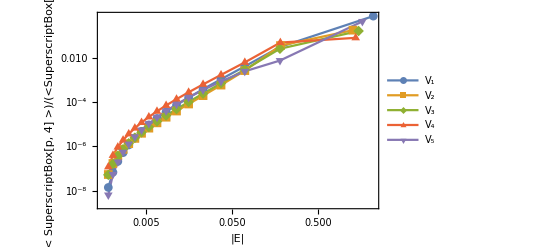

```mathematica
ListLogLogPlot[MapThread[Transpose[{-#1}~Join~{#2}]&,{en,p4error}],Joined->True,Frame->True,ImageSize->Full,PlotMarkers->Automatic,PlotLegends->{"V_1","V_2","V_3","V_4","V_5"},FrameLabel->{"|E|","|(Δ < SuperscriptBox[p, 4] >)/(<SuperscriptBox[p, 4]>)|"},RotateLabel->False,Axes->False,PlotRange->Full]
Export["C:\\Users\\ASUS\\OneDrive\\Documents\\Test_6\\MultiplePotential_8.eps",%];
```

```mathematica
ψ0True={{-2.600286643079845,0.1821787908204444,0.09419781206069973,0.05897725156884739,0.04123055023831362,0.030873538991778776,0.02422260666350586,0.01965640583056356,0.01636307357741776,0.013896147961756356,0.011992009377176878,0.010486056760412674,0.009270777945683309,0.008273292810255694,0.007442634994919214,0.00674220594686196,0.006145117868693646,0.005631220853812926,0.005185148585196758,0.004795000233280505},{-3.4055081176236937,0.3691170996432108,0.18296280370302045,0.11340138245937312,0.07896141590769379,0.05900860313035081,0.046243915071287285,0.03749973577976831,0.031202000582528918,0.026489106712104315,0.022853859705868777,0.019980244109494456,0.017662165615213877,0.015760078061311248,0.014176480617576627,0.01284140733896176,0.011703485034506035,0.010724231709216976,0.009874311938164326,0.009131013237679541},{-3.875449023850947,0.3425167762624806,0.17371522523731667,0.10820114616774769,0.0754786955791382,0.056455716778468466,0.044265104339331736,0.035906035128157085,0.02988198018675555,0.02537204578560584,0.021892345084313376,0.019141105202838706,0.016921389858155653,0.015099788253372106,0.013583051395591824,0.012304244829067874,0.011214209815447327,0.010276116149885113,0.009461883230528167,0.008749767281632018},{-2.720259298411899,0.2784326425352952,0.13940829842269842,0.08654339859963503,0.06028782814591442,0.045061682047307934,0.03531689677821949,0.02864012300970136,0.023830862267865627,0.020231639497282745,0.01745530446702276,0.015260592048086307,0.013490138512830228,0.01203738445036483,0.010827872642216498,0.009808170913199878,0.008939045001187085,0.008191105122063346,0.007541946607314545,0.006974222771247559},{-2.8694855973846614,0.25202428188209786,0.12705702804659444,0.07910066251638072,0.055179264934929396,0.041274774712102155,0.03236386174273911,0.02625322987573763,0.02184924902146716,0.01855201680150591,0.01600788835991059,0.013996298498418424,0.01237329665532475,0.011041360176767087,0.009932320902168631,0.008997245318700421,0.008200193781105695,0.0075142391300266655,0.0069188506361425916,0.006398130296317194}};
```

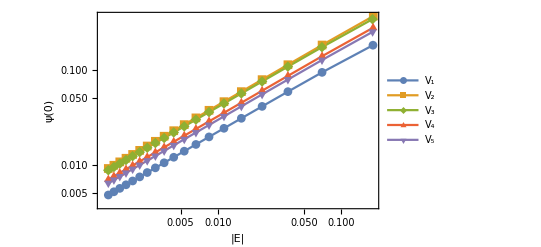

```mathematica
ListLogLogPlot[MapThread[Transpose[{-#1}~Join~{#2}]&,{en,ψ0True}],Joined->True,Frame->True,ImageSize->Full,PlotMarkers->Automatic,PlotLegends->{"V_1","V_2","V_3","V_4","V_5"},FrameLabel->{"|E|","ψ(0)"},RotateLabel->False,Axes->False,PlotRange->Full]
Export["C:\\Users\\ASUS\\OneDrive\\Documents\\Test_6\\MultiplePotential_9.eps",%];
```

```mathematica
ψ0error={{3.11361339936413,0.03719559283806232,0.005173565967008055,0.001422014024754787,0.0005334363021966017,0.0002384755155905678,0.00011893830550245742,0.0000637202179921073,0.000035778607906090506,0.000020679101116813635,0.000012139817661129505,7.117908278817565*^-6,4.118536176288032*^-6,2.317518191075992*^-6,1.2277387884449055*^-6,5.84798045354007*^-7,2.3704236358056523*^-7,5.906398906989529*^-8,7.965722306126733*^-10,7.938385477111518*^-10},{3.270235536906508,0.03620084518740817,0.0037554240376992403,0.0009213154592797135,0.00031979427505815153,0.00013463920330669487,0.00006394190370168535,0.000032866790340014246,0.000017803508862669418,9.964032152037256*^-6,5.676003042150637*^-6,3.2396064889177743*^-6,1.8248940790333122*^-6,9.947191542083043*^-7,5.104820648109476*^-7,2.2954967999329038*^-7,8.14831378051095*^-8,1.128230894313095*^-8,1.395386000467596*^-9,1.3919022187855701*^-9},{3.244452728748031,0.027916334283097,0.003534496272153431,0.0009031100937945122,0.0003201247546962103,0.00013687310972387634,0.00006590375459293672,0.000034354929857229955,0.00001889979657566311,0.00001077268866136324,6.272633401427075*^-6,3.6837406873006513*^-6,2.159071002567961*^-6,1.2416258514426105*^-6,6.888347967514906*^-7,3.57644637203018*^-7,1.684909818461864*^-7,6.265455067573133*^-8,8.127380625339697*^-10,8.101962937011786*^-10},{3.472204634557504,0.04297784778069177,0.005851039908424045,0.0016243126242754308,0.0006168873634248128,0.0002788788995176238,0.000140416432840362,0.00007579807683162206,0.00004281781857441943,0.000024852881098818884,0.00001463123768740008,8.598229691373424*^-6,4.9657662521136125*^-6,2.791188741270964*^-6,1.46070632762793*^-6,6.881039347171741*^-7,2.556313423704409*^-7,3.8847502939572096*^-8,9.45781983695427*^-10,9.43085475642333*^-10},{3.6874584603514866,0.01341248591511228,0.0006951646977625089,0.000026145119960311007,0.00007142126089741974,0.0000535179782609319,0.00003530510094352456,0.00002266403059660156,0.000014442594858771958,9.157022488850602*^-6,5.7579111796243255*^-6,3.5573713063640996*^-6,2.1379409666041827*^-6,1.2184973215285468*^-6,6.41831719703287*^-7,2.98802016001955*^-7,9.933947882473961*^-8,4.633297356919448*^-9,1.4717306539980551*^-9,1.4679124723071103*^-9}};
```

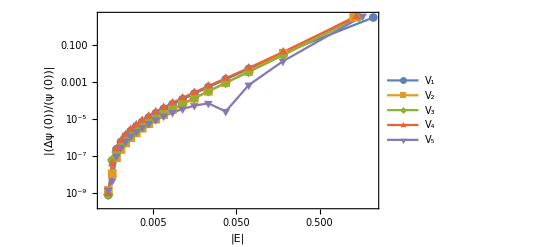

```mathematica
ListLogLogPlot[MapThread[Drop[Transpose[{-#1}~Join~{#2}],-1]&,{en,ψ0error}],Joined->True,Frame->True,ImageSize->Full,PlotMarkers->Automatic,PlotLegends->{"V_1","V_2","V_3","V_4","V_5"},FrameLabel->{"|E|","|(Δψ (0))/(ψ (0))|"},RotateLabel->False,Axes->False,PlotRange->Full]
Export["C:\\Users\\ASUS\\OneDrive\\Documents\\Test_6\\MultiplePotential_10.eps",%];
```

```mathematica
c1a=Import["D:\\Documents\\aDependence\\c1aV1.dat","CSV"];
```

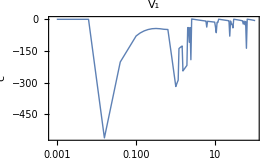

```mathematica
ListLogLinearPlot[c1a,ImageSize->270,Frame->True,Joined->True,PlotRange->All,Axes->False,FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{"c",None},{"a",None}},PlotStyle->Thick,PlotLabel->Style["V_1",15],RotateLabel->False,FrameTicksStyle->{{{Bold,11},{}},{{Bold,11},{}}}]
Export["C:\\Users\\yingsheng\\OneDrive\\Documents\\Test_6\\V1_c1_veus_a.eps",%];
```

```mathematica
c1a=Import["D:\\Documents\\aDependence\\c1aV4.dat","CSV"];
```

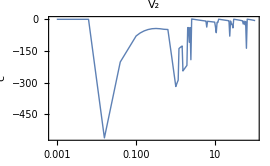

```mathematica
ListLogLinearPlot[c1a,ImageSize->270,Frame->True,Joined->True,PlotRange->All,Axes->False,FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{"c",None},{"a",None}},PlotStyle->Thick,PlotLabel->Style["V_4",15],RotateLabel->False,FrameTicksStyle->{{{Bold,11},{}},{{Bold,11},{}}}]
Export["C:\\Users\\yingsheng\\OneDrive\\Documents\\Test_6\\V2_c1_veus_a.eps",%];
```

```mathematica
c1a=Import["D:\\Documents\\aDependence\\c1aV5.dat","CSV"];
```

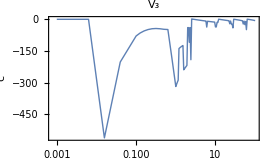

```mathematica
ListLogLinearPlot[c1a,ImageSize->270,Frame->True,Joined->True,PlotRange->All,Axes->False,FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{"c",None},{"a",None}},PlotStyle->Thick,PlotLabel->Style["V_5",15],RotateLabel->False,FrameTicksStyle->{{{Bold,11},{}},{{Bold,11},{}}}]
Export["C:\\Users\\yingsheng\\OneDrive\\Documents\\Test_6\\V3_c1_veus_a.eps",%];
```